```mathematica
generatePin[]:=Module[{x1, x2, y1, y2, theta},
x1=Random[];
y1=Random[];
theta = 2*Pi*Random[];
x2=x1+Cos[theta];
y2 = y1 + Sin[theta];
{{x1, y1}, {x2, y2}}]
```

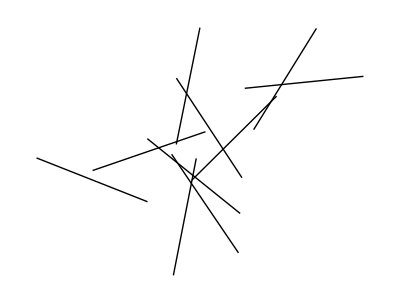
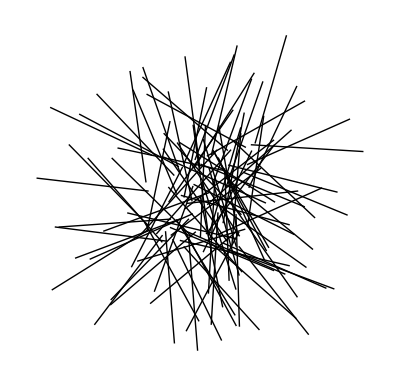
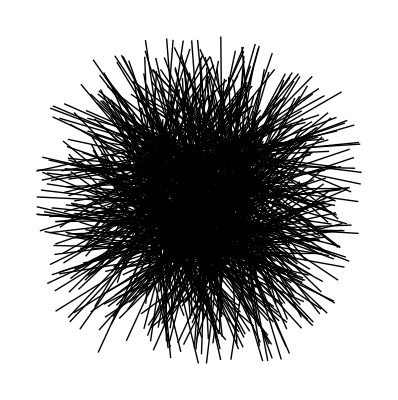
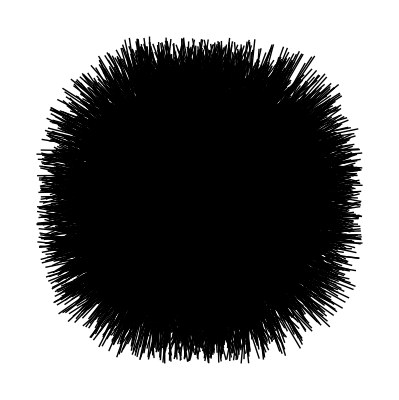

```mathematica
Graphics[{Line[generatePin[]]&/@Range[10^#]}]&/@Range[4]
```

```mathematica
What is the density of lines above?
```

```mathematica
pin = generatePin[]
```

{{0.981881,0.122689},{0.179222,0.719128}}

```mathematica
checkCrosses[pin_]:=Module[{},
{{x1, y1}, {x2, y2}} = pin;
xCross=Abs[Floor[x1]-Floor[x2]];
yCross = Abs[Floor[y1]-Floor[y2]];
{xCross, yCross}]
```

```mathematica
data=Total[checkCrosses[generatePin[]]]&/@Range[100000];
```

```mathematica
Length[Select[data, #==0 &]]
```

4592

```mathematica
Length[Select[data, #==1&]]
```

63716

```mathematica
Length[Select[data, #==2&]]
```

31692

```mathematica
0.0459/N[1-Pi/4]
```

0.213884

```mathematica
generatePin[xMax_, yMax_, xMin_, yMin_]:=Module[{x1, x2, y1, y2, theta},
x1=xMin+(xMax-xMin)*Random[];
y1=yMin+ (yMax-yMin)*Random[];
theta = 2*Pi*Random[];
x2=x1+Cos[theta];
y2 = y1 + Sin[theta];
{{x1, y1}, {x2, y2}}]
```

```mathematica
compute[x_, y_]:=Module[{},
NN=1000;
dats=Total[checkCrosses[generatePin[x, y, x-0.01, y-0.01]]]&/@Range[NN];
N[Length[Select[dats, #==0 &]]/NN]]
```

```mathematica
results=Table[Table[{N[x/100], N[y/100], compute[x/100, y/100]}, {x, 1, 100}], {y,1, 100}];
```

```mathematica
(* Plots the probability that the rod falls within the square *)
```

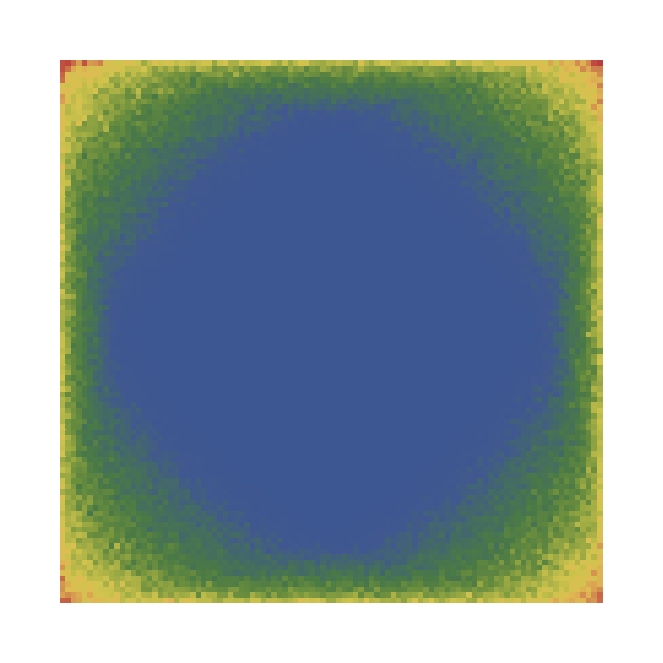

```mathematica
Graphics[{ColorData["DarkRainbow"][N[#[[3]]]/.25], Rectangle[{#[[1]], #[[2]]}, {#[[1]]+0.01, #[[2]]+0.01}]}&/@Partition[Flatten[results], 3]]
```

```mathematica
Graphics
```

```mathematica
Max[#[[3]]&/@Partition[Flatten[results], 3]]
```

0.154

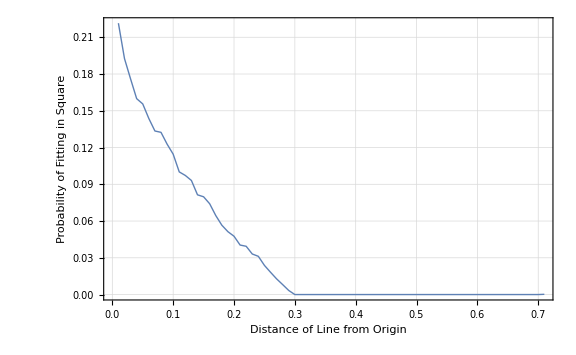

```mathematica
ListPlot[results[[1;;71]], Joined->True, Frame ->True,FrameStyle->Directive[14], GridLines->Automatic, PlotStyle->Thick, FrameLabel->{"Distance of Line from Origin", "Probability of Fitting in Square"}, ImageSize->Large ]
```